```mathematica
(*Mathematica notebook to generate GCL connectivity
Guy Billings 2013*)
```

```mathematica
(*SetDirectory so that file works from within DropBox using the Code version in DropBox*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory["../../Code/GCL-Mathematica-toolbox/"]
```

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Code/GCL-Mathematica-toolbox

```mathematica
(*Import library functions related to the TissueModel*)
Import["TissueModel.m"]
```

```mathematica
(*Diameter of tissue ball in microns*)
Diam=80;
```

```mathematica
(*SeedRandom[1*Round[Date[][[6]]]]*)
(*Number MFs populating the larger embedding volume. Should not need to change*)
nummf=2745; 
(*Number of connections for each GRC*)
d=4;
(*Dimensions of the embedding geometry: eg. side length if embedding geom is a cube*)
biglen=200;
(*Empirical distribution of glom per MF, taken from Sultan, does not have any material affect given the connectivity settings used - ask me about it if you want to know what that means - but it need to be here nevertheless*)
rdist={45,17,8,5};
(*glomerular x-spacing*)
glox=60;
(*glomerular y-spacing*)
gloy=20;
(*glomerular z-spacing*)
gloz=2;
(*embedding geometry. should not need to change*)
embedinggeom="cube";
(*geometry of the local network. shold not need to change*)
samplegeom="sphere";
(*target soft-constrained dnedrite length*)
dlen=15;
(*spatial scale of random exponentially distributed input correlations*)
corr=0;
```

```mathematica
(*compute positions of cells*)
glomraw=glopos[biglen,nummf,rdist,glox,gloy,gloz,embedinggeom];
glompos=DeleteCases[confineglom[glomraw,samplegeom,Diam],{}];
granpos=grcpos[biglen,Diam,grcinvol[Diam,samplegeom],samplegeom];


(*should not need to change the final 2 flags ('mossyrepeat' and 'force')*)
connsM=ALGconnections[dlen,glompos,granpos,d,2,1];

(*compute adjacency matrix*)
AmodelM=Amatrix[connsM[[1]]];

(*plot adjacency matrix between gloms and grcs*)
MatrixPlot[AmodelM[[2]], ColorFunction->"Monochrome"]

(*plot adjacency matrix between mfs and grcs*)
MatrixPlot[AmodelM[[4]], ColorFunction->"Monochrome"]
```

-Graphics-

-Graphics-

```mathematica
outputfile = NotebookDirectory[]<>"GCLconnectivity.graphml"
```

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev/GCLconnectivity.graphml

```mathematica
(*export to graphml*)
Export[outputfile,AmodelM[[4]]];
```

```mathematica
(*output glom. and GC position information*)
outputfile = NotebookDirectory[]<>"GLOMpositions.csv";
Export[outputfile,Flatten[glompos, 1]]
outputfile = NotebookDirectory[]<>"GCpositions.csv";
Export[outputfile,granpos]
```

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev/GLOMpositions.csv

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev/GCpositions.csv

```mathematica
(*Visual check of the connectivity:*)
```

```mathematica
(*glom. degree distribution*)
```

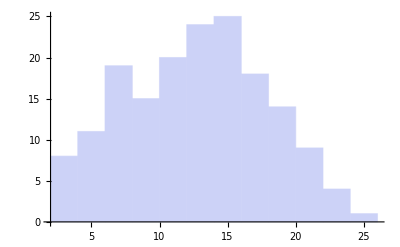

```mathematica
Histogram[Total[AmodelM[[3]]]]
```

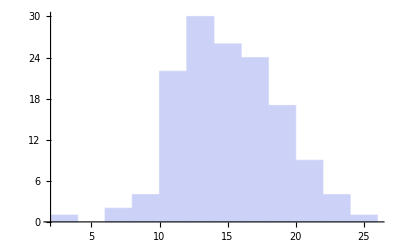

```mathematica
(*mf degree distribution*)
Histogram[Total[AmodelM[[1]]]]
```

```mathematica
?denlendist
```

denlendist[conns_, glompos_, granpos_] Distribution of granule cell dendrite length.

```mathematica
dlendist=denlendist[connsM[[1]],glompos,granpos];
```

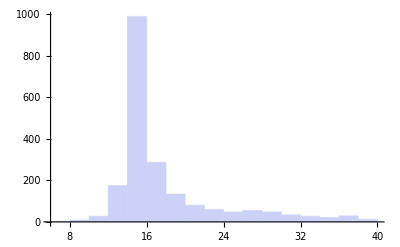

```mathematica
Histogram[Flatten[dlendist]]
```

```mathematica
GRAglom=Graphics3D[{Blue,Point[Flatten[glompos,1]]}];
```

```mathematica
GRAgrc=Graphics3D[{Red,PointSize[Large],Point[granpos]}];
```

```mathematica
Show[GRAglom,GRAgrc]
```

-Graphics3D-

-Graphics3D-